```mathematica
Z=1;
a0 = 5.29177210544×10^-11;   (*Bohr radius *)
c=299792458; (* Speed of light *)
Eh=4.3597447222060*10^−18;
Ry =Eh/2; (* Rydberg energy *) 
hbar=1.054571817*10^−34;
h=6.62607015*10^−34;
```

```mathematica
Get["D:\\thesis\\mathematica\\dipole_moments\\dipolemoments.m"];
```

```mathematica
Radialdpup[n_, l_, k_,lprime_] := Module[{gValue, lmax},
    lmax = Max[l, lprime];
    gValue = gup[n-l][n, k]/Sqrt[Rho[k]]; 
    (* Full formula *)
   gValue
]
```

```mathematica
Radialgup[n_, l_, W_,lprime_] := Module[{gValue, lmax,k},
    lmax = Max[l, lprime];
k=Sqrt[W/Ry];
    gValue = gup[n-l][n, k]; 
    (* Full formula *)
   gValue
]
```

gup::numk: -- Message text not found -- (1. √W)

General::stop: Further output of gup::numk will be suppressed during this calculation.

General::munfl: Exp[-1554.23] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

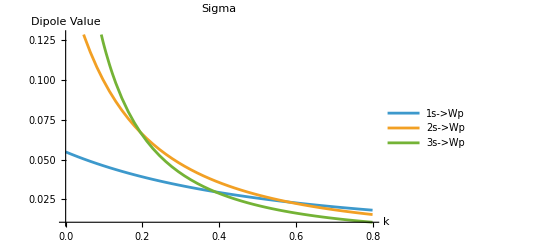

```mathematica
Plot[Evaluate[{Radialgup[1,0,W Ry,1],Radialgup[2,0,W Ry,1],Radialgup[3,0,W Ry,1]}], {W, 0, 0.8},
 PlotLabel -> "Sigma",
 AxesLabel -> {"k", "Dipole Value"},
 PlotLegends -> {"1s->Wp","2s->Wp","3s->Wp"},
 PlotRange ->{Automatic, Automatic}]
```

```mathematica
Radialgup2[n_, l_, W_,lprime_] := Module[{gValue, lmax,k},
    lmax = Max[l, lprime];
k=Sqrt[W/Ry];
    gValue = gup[n-l][n, k]; 
    (* Full formula *)
   Abs[gValue]^2
]
```

```mathematica
Sigma[n_, l_, W_,lprime_] := Module[{gValue, lmax,w},
    lmax = Max[l, lprime];
    w=(W+Ry/n^2)/hbar;
    gValue = gup[n-l][n, Sqrt[W/Ry]]; (*MISTAKE if lprime<l use gdown*)
    (* Full formula *)
   (4*π^2*w*a0*2*Ry)/(3*c) *10^4 (lmax/(2*l + 1))* Abs[gValue]^2
]
```

Reproducing L. M. Ugray and R. C. Shiell’s results

gup::numk: -- Message text not found -- (1. √W)

General::stop: Further output of gup::numk will be suppressed during this calculation.

General::munfl: Exp[-9829.83] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

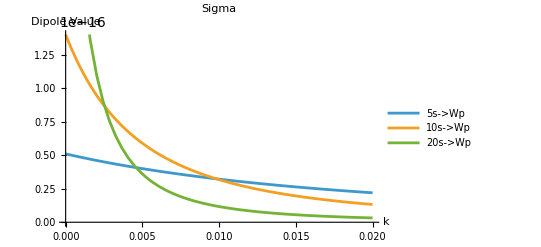

```mathematica
PP=Plot[Evaluate[{Sigma[5,0,W Ry,1],Sigma[10,0,W Ry,1],Sigma[20,0,W Ry,1]}], {W, 0, 0.02},
 PlotLabel -> "Sigma",
 AxesLabel -> {"k", "Dipole Value"},
 PlotLegends -> {"5s->Wp","10s->Wp","20s->Wp"},
 PlotRange ->{Automatic, {0,14*10^-17}}]
```

```mathematica
eE0=Sqrt[h];
Ei[i_]:=-Ry/i^2;
ωi[i_]:=Ei[i]/hbar;
(*T[w_]:=100;*)
SumPWOmega2up[n_, l_, W_]:=eE0^2*n^4/Z^4*Sum[((l+1)^2-m^2)/(4(l+1)^2-1),{m,-l,l}]* Abs[gup[n-l][n, Sqrt[W/Ry]]]^2;
SumPWOmega2down[n_, l_, W_]:=eE0^2*n^4/Z^4*Sum[(l^2-m^2)/(4l^2-1),{m,-l,l}]* Abs[gdown[n-l][n, Sqrt[W/Ry]]]^2;
```

```mathematica
lambda[w_]:=2*Pi*c/w;
wfromlam[L_]:=2*Pi*c/L;
```

```mathematica
sincTerm[W_, ω_,i_,T_] := Sinc[((W- Ei[i])/hbar - ω)/2 * T]^2
```

```mathematica
ωmin = 0;
ωmax =- 1.5*Ei[1]/hbar;
lambdamin=lambda[ωmax]
lambdamax=lambda[-Ei[2]/(1.2*hbar)]
```

6.07511×10^-8

4.37408×10^-7

```mathematica
lambda[-Ei[1]/(hbar)]
```

9.11267×10^-8

```mathematica
lambda[-Ei[2]/(hbar)]
```

3.64507×10^-7

Case 1 : 1s and 2s

```mathematica
integrand[W_, ω_,T_] :=  T^2/(2*hbar^2) (SumPWOmega2up[1, 0, W]sincTerm[W, ω,1,T]+SumPWOmega2up[2, 0, W]sincTerm[W,ω,2,T])

Pni[ω_?NumericQ, T_?NumericQ] := NIntegrate[integrand[W, ω,T], {W, 0, (ω+10*2Pi/T)hbar}]
```

```mathematica
Plot[sincTerm[0, w,1,100 2Pi/w], {w, ωmin,ωmax}]
```

-Graphics-

```mathematica
(* Plot range *)

data1 = Table[{L, Pni[wfromlam[L],100L/c]}, {L, lambdamin, lambdamax, (lambdamax - lambdamin)/100}]; (* 100 points *)
(*Export["Pni_data_M=2T=100_v0.wl", data, "WL"];  Wolfram Language format *)
```

gup::numk: -- Message text not found -- (6.77305×10^8 √W)

General::stop: Further output of gup::numk will be suppressed during this calculation.

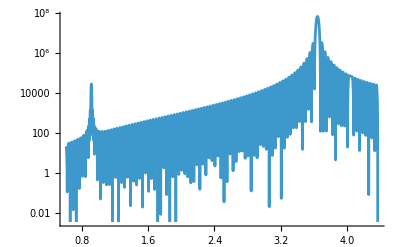

Exports/IntegrandwrtLam_1s2s_T=100tp_E0e=sqrth_May2.png

```mathematica
P=LogPlot[integrand[0,wfromlam[L],100L/c], {L, lambdamin,lambdamax}]
```

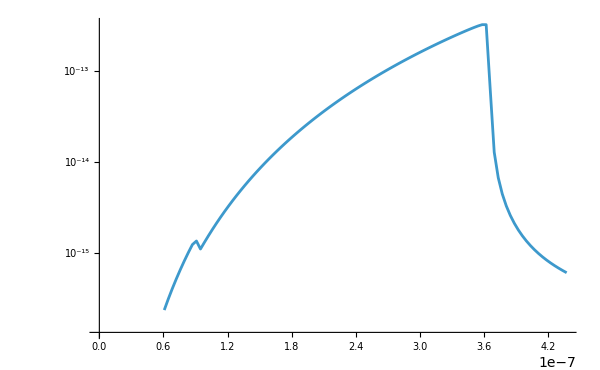
-Graphics-λ

Exports/IPwrtLam_1s2s_T=100tp_E0e=sqrth_May2.png

```mathematica
(* Plot Pni(ω) *)
P = Labeled[
  ListLogPlot[data1, 
 ImageSize -> 600,Joined -> True],
  Style["λ",  FontSize -> 20],
  Bottom
]
```

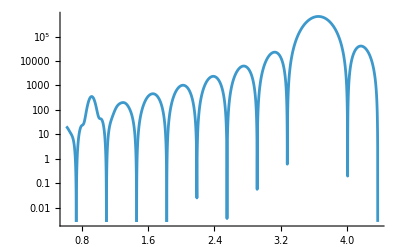

Exports/IntegrandwrtLam_1s2s_T=10tp_E0e=sqrth_May2.png

```mathematica
P=LogPlot[integrand[0,wfromlam[L],10L/c], {L, lambdamin,lambdamax}]
```

gup::numk: -- Message text not found -- (6.77305×10^8 √W)

General::stop: Further output of gup::numk will be suppressed during this calculation.

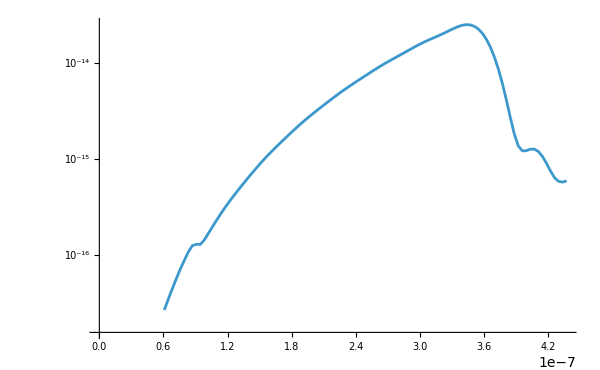
-Graphics-λ

Exports/IPwrtLam_1s2s_T=10tp_E0e=sqrth_May2.png

Exports/IntegrandwrtLam_1s2s_T=1000tp_E0e=sqrth_May2.png

```mathematica
P=Labeled[
  ListLogPlot[Table[{L, Pni[wfromlam[L],10L/c]}, {L, lambdamin, lambdamax, (lambdamax - lambdamin)/100}], 
 ImageSize -> 600,Joined -> True],
  Style["λ",  FontSize -> 20],
  Bottom
]
```

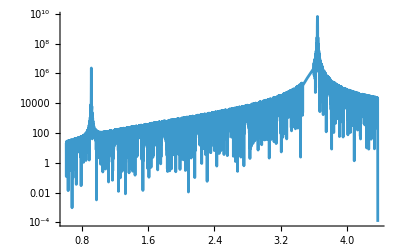

```mathematica
P=LogPlot[integrand[0,wfromlam[L],1000L/c], {L, lambdamin,lambdamax}]
```

gup::numk: -- Message text not found -- (6.77305×10^8 √W)

General::stop: Further output of gup::numk will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in W near {W} = {2.72839×10^-18}. NIntegrate obtained 2.31247×10^-15 and 5.80931×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in W near {W} = {2.53873×10^-18}. NIntegrate obtained 3.06092×10^-15 and 6.76413×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in W near {W} = {2.37×10^-18}. NIntegrate obtained 3.99334×10^-15 and 7.56835×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

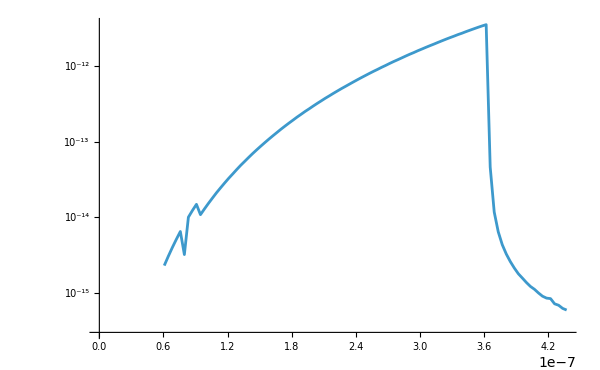
-Graphics-λ

```mathematica
P=Labeled[
  ListLogPlot[Table[{L, Pni[wfromlam[L],1000L/c]}, {L, lambdamin, lambdamax, (lambdamax - lambdamin)/100}], 
 ImageSize -> 600,Joined -> True],
  Style["λ",  FontSize -> 20],
  Bottom
]
```

```mathematica
cm = 72/2.54 ;(* centimetre *)
Export["Exports/IPwrtLam_1s2s_T=1000tp_E0e=sqrth_May2.png",P, "png",ImageResolution -> 300]
```

Exports/IPwrtLam_1s2s_T=1000tp_E0e=sqrth_May2.png